## ShapeMatrix and HoppingGraph

```mathematica
(*The size of the matrix and internal dimension on each site*)
lx=14; ly=14;
internalDimension=2;

(*List of all coordinates in the matrix*)
coordinateList = Flatten[Table[{i,j},{i,1,lx},{j,1,ly}],1]; 
	
(*Select all sites belonging to a given shape*)
coordInShape=Select[coordinateList,#∈Polygon[{{1,1},{lx,1},{lx,ly},{1,ly}}]&];

(*size: number of sites in the given shape*)
size=Length[coordInShape];

(*n: number of d.o.f in the QWZ model*)
n=size * internalDimension;

(*Constructing a shape matrix, 1 for sites in the shape and 0 for sites outside the shape*)
shapeMatrix = SparseArray[({#[[1]],#[[2]]}->1)&/@coordInShape,{lx,ly},0];

(*List of directions*)
directions={{-1,0},{1,0},{0,-1},{0,1},{0,0}};

hoppingMatrix=Table[
	Module[{sa,edges,onesPositions},
	sa=shapeMatrix;
	onesPositions =coordInShape;

	(*Choosing # -> # + direc if # + direc is in onesPositions*)
	edges =(#->#+direc)&/@Select[onesPositions,MemberQ[onesPositions,#+direc]&];
	(*using onesPositions as vertexCoordinates, and edges as edges, paint the graph.1*)
	Transpose@AdjacencyMatrix@Graph[onesPositions,edges,VertexCoordinates->onesPositions,DirectedEdges->True,EdgeStyle->Red,VertexSize->Large,ImageSize->600]
	],
{direc,directions}
];
```

## Hamiltonian

```mathematica
(*Parameters*)
μ=1; γ=0.0; 

(*Bloch Hamiltonian*)
hk[kx_,ky_]:=(μ-Cos[kx]-Cos[ky])PauliMatrix[3]+(Sin[kx]+I γ)PauliMatrix[1]+(Sin[ky]+I γ)PauliMatrix[2]; 
(* Hamiltonian in non-Hermitian Chern bands.*)

(*Substitution for Bloch Hamiltonian: one can prove that coefficient of ⅇ^Subscript[ik, x] term corresponds to the |Subscript[m, x+1],Subscript[m, y]><Subscript[m, x],Subscript[m, y]| term,
and the direction of adjacency matrix of a diagram is reverse to that of tight binding models. So we need to Transpose the AdjacencyMatrix*)


(*Extracting hopping coefficients*)
hβ[x_,y_]:=TrigToExp[hk[kx,ky]]/.{Exp[I kx]->x,Exp[-I kx]->1/x,Exp[I ky]->y,Exp[-I ky]->1/y};
hoppingCoeff=Coefficient[Coefficient[hβ[βx,βy],βx,#[[1]]],βy,#[[2]]]&/@directions;
obcHamiltonian = Sum[KroneckerProduct[hoppingMatrix[[i]],hoppingCoeff[[i]]],{i,1,Length@hoppingCoeff}];

(*Solving OBC Hamiltonian*)
eigsys=Eigensystem[N[obcHamiltonian]];
eigvalues=eigsys[[1]];
eigvectors = eigsys[[2]];
Clear[eigsys];
```

Eigensystem::arh: 因为在 392 个特征值和/或特征向量中找到 392 个，利用稠密矩阵方法速度更快，稀疏输入矩阵将被转化. 如果较少的特征值和/或特征向量是充分的，那么考虑利用 Eigensystem 的第二个参数限制这个数目.

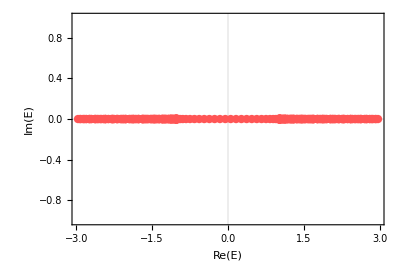

```mathematica
P0=Show[ListPlot[ReIm[Chop[eigvalues]],PlotStyle->{Lighter@Red,PointSize[0.015]},PlotTheme->"Scientific",Frame->True,FrameStyle->Black,FrameTicksStyle->{18,18},FrameLabel->{Style["Re(E)",18],Style["Im(E)",18]},PlotRange->All,ImageSize->400,AspectRatio->2/3]]
```

```mathematica
(*回去推导一下整个过程，写一个note*)
```

## Green Function

```mathematica
listOfCurrent[w_]:=
Module[{},
gf=Inverse[w IdentityMatrix[n] - N[obcHamiltonian]];
gaa = Table[gf[[2i-1,2j-1]],{i,1,size},{j,1,size}];
gab = Table[gf[[2i-1,2j]],{i,1,size},{j,1,size}];
gba = Table[gf[[2i,2j-1]],{i,1,size},{j,1,size}];
gbb = Table[gf[[2i,2j]],{i,1,size},{j,1,size}];
gs=Table[hoppingCoeff[[i]][[1,1]]*gaa+hoppingCoeff[[i]][[1,2]]*gba+hoppingCoeff[[i]][[2,1]]*gab+hoppingCoeff[[i]][[2,2]]*gbb,{i,1,Length@hoppingCoeff}];
(*1:-1,0; 2:1,0; 3:0,-1; 4:0,1*)
js=Sum[I/2(gs[[i]].hoppingMatrix[[i]]+hoppingMatrix[[i]].gs[[i]])#&/@directions[[i]],{i,1,Length@hoppingCoeff}];
Table[{js[[1]][[m,m]],js[[2]][[m,m]]},{m,1,size}]];
```

-0.0532665

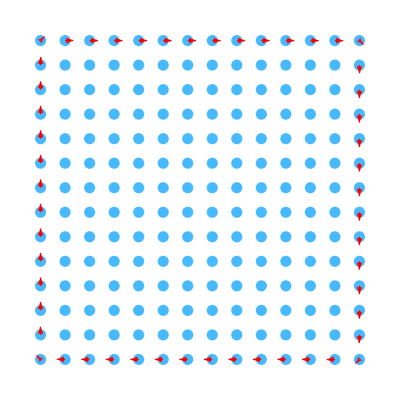

```mathematica
n1=n;
η=0.0001;

ω=eigvalues[[n1]]
currentTable = -η listOfCurrent[eigvalues[[n1]]- η];
(*Plot*)
currentTable1=Re@currentTable;
maxcurrent1 = Max[Norm[#]&/@currentTable1];
wavdat1=Table[{currentTable1[[i]],coordInShape[[i]]},{i,1,size}];
currentDiagram =
Show[Graphics[{RGBColor[0.2,0.7,1],PointSize[0.02],Opacity[.9],Point[#[[2]]]}&/@wavdat1],Graphics[{Opacity[Norm[#[[1]]]/maxcurrent1],Red,Arrowheads[Norm[#[[1]]]*3],Thick,Arrow[{#[[2]],20#[[1]]+#[[2]]}]}&/@wavdat1]]
```

```mathematica
currentTable//Dimensions
```

{196,2}

```mathematica
j//Dimensions
```

{196,2}

## Plot Current Exp Values (incorrect in non-Hermitian case) because of non-orthogonality

```mathematica
(*List of jx at every site, cf. note*)
jxlist = Table[
Module[{},
site=SparseArray[{i,i}->1,{size,size}];	
jxm=KroneckerProduct[-I( hoppingMatrix[[2]].site+site.hoppingMatrix[[2]]),(PauliMatrix[3]+I PauliMatrix[1])/2];
jxm+=ConjugateTranspose[jxm] (*+h.c.*)
],{i,1,size}];

jylist = Table[
Module[{},
site = SparseArray[{i,i}->1,{size,size}];
jym=KroneckerProduct[-I( hoppingMatrix[[4]].site+site.hoppingMatrix[[4]]),(PauliMatrix[3]+I PauliMatrix[2])/2];
jym+=ConjugateTranspose[jym] (*+h.c.*)
],{i,1,size}];
```

-0.0532665

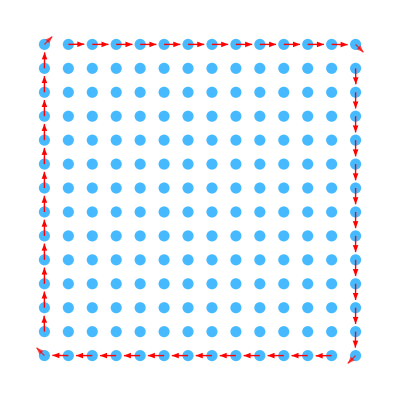

```mathematica
(*Plot Current at every site for a certain eigenstate*)
eigvalues[[n1]]
wav = eigvectors[[n1]];

(*The current expectation value at every site*)
currentTablex = Table[ConjugateTranspose[wav].jxlist[[i]].wav,{i,1,size}];
currentTabley = Table[ConjugateTranspose[wav].jylist[[i]].wav,{i,1,size}];
currentTable =Chop[Re@Transpose[{currentTablex,currentTabley}],10^-7];
maxcurrent = Max[Norm[#]&/@currentTable];
wavdat=Table[{currentTable[[i]],coordInShape[[i]]},{i,1,size}];
currentDiagram =
Show[Graphics[{RGBColor[0.2,0.7,1],PointSize[0.02],Opacity[.9],Point[#[[2]]]}&/@wavdat],Graphics[{Opacity[Norm[#[[1]]]/maxcurrent],Red,Arrowheads[Norm[#[[1]]]*3],Thick,Arrow[{#[[2]],20#[[1]]+#[[2]]}]}&/@wavdat]]
```

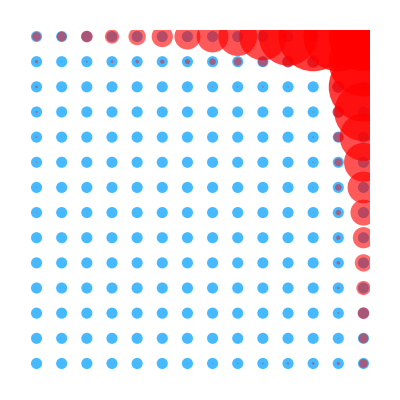

```mathematica
(*Plot density*)
wavsum=Chop@Sqrt[Abs[eigvectors[[n1]][[1;;n;;2]]]^2+Abs[eigvectors[[n1]][[2;;n;;2]]]^2];
wavdat=Table[{wavsum[[i]],coordInShape[[i]]},{i,1,Length@wavsum}];
Plotwavdk=Show[Graphics[{RGBColor[0.2,0.7,1],PointSize[0.02],Opacity[.9],Point[#[[2]]]}&/@wavdat],Graphics[{Red,Opacity[(#[[1]])^(1/5)],PointSize[(#[[1]])/2],Point[#[[2]]]}&/@wavdat]]
```

## Skin Effect

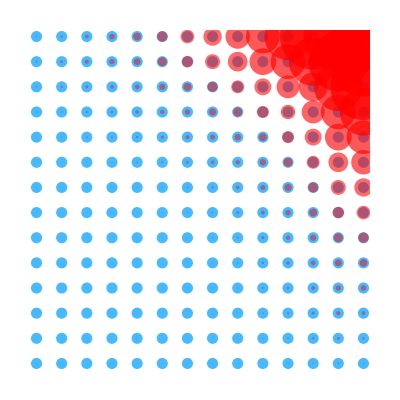

```mathematica
wav=Table[Abs[eigvectors[[j,i]]]+Abs[eigvectors[[j]][[i+1]]],{i,1,n,2},{j,1,n}];
wavsum=Normalize[Sum[wav[[;;,j]],{j,1,n}]];
wavdat=Table[{wavsum[[i]],coordInShape[[i]]},{i,1,size}];
Plotwavdk=Show[Graphics[{RGBColor[0.2,0.7,1],PointSize[0.02],Opacity[.9],Point[#[[2]]]}&/@wavdat],Graphics[{Red,Opacity[(#[[1]])^(1/5)],PointSize[(#[[1]])/2],Point[#[[2]]]}&/@wavdat]]
```